# Analiza borznega tečaja delnice KRKG (2025)

## Pridobivanje podatkov

Podjetje KRKA je slovensko farmacevtsko podjetje, ki razvija, proizvaja in trži zdravila ter druge farmacevtske izdelke. Delnica podjetja kotira na Ljubljanski borzi pod oznako KRKG. V nadaljevanju bom analiziral gibanje njenega borznega tečaja za leto 2025.

```mathematica
SetDirectory[NotebookDirectory[]];

data=Import["KRKG_2025.xlsx"];

dates=DateObject/@data[[1,2;;,4]];
last=data[[1,2;;,9]];
volume=data[[1,2;;,13]];
trades=data[[1,2;;,12]];

dates=Reverse[dates];
last=Reverse[last];
volume=Reverse[volume];
trades=Reverse[trades];

Grid[{{"Lastnost","Podatek"},{"Ime podjetja","Krka, d. d., Novo mesto"},{"Sedež","Novo mesto, Slovenija"},{"Panoga","Mednarodno generično farmacevtsko podjetje"},{"Borzna oznaka","KRKG"},{"Prihodki od prodaje (2025)","2,041 milijarde EUR"},{"Čisti dobiček (2025)","403,7 milijona EUR"},{"Prisotnost","Več kot 70 držav"},{"Zaposleni","12.753"},{"Proizvodni obrati v Sloveniji","Novo mesto (Ločna, Bršljin), Krško, Šentjernej, Ljutomer"},{"Proizvodno-distribucijski centri","Rusija, Poljska, Hrvaška, Nemčija"}},Frame->All,Background->{None,{LightGray,None}},Alignment->Left]
```

Lastnost | Podatek
Ime podjetja | Krka, d. d., Novo mesto
Sedež | Novo mesto, Slovenija
Panoga | Mednarodno generično farmacevtsko podjetje
Borzna oznaka | KRKG
Prihodki od prodaje (2025) | 2,041 milijarde EUR
Čisti dobiček (2025) | 403,7 milijona EUR
Prisotnost | Več kot 70 držav
Zaposleni | 12.753
Proizvodni obrati v Sloveniji | Novo mesto (Ločna, Bršljin), Krško, Šentjernej, Ljutomer
Proizvodno-distribucijski centri | Rusija, Poljska, Hrvaška, Nemčija

Spodnji graf prikazuje gibanje zaključne cene (Last Price) delnice KRKG skozi leto 2025. Iz grafa lahko razberemo spremembe borzne cene skozi čas ter opazujemo obdobja rasti, padcev in večjih nihanj tečaja.

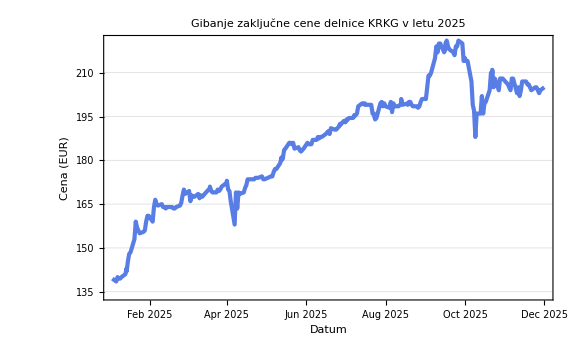

```mathematica
DateListPlot[Transpose[{dates,last}],PlotTheme->"Business",ImageSize->Large,PlotLabel->"Gibanje zaključne cene delnice KRKG v letu 2025",AxesLabel->{"Datum","Cena (EUR)"},Joined->True]
```

Iz grafa je razvidno, da je tečaj delnice v prvi polovici leta postopoma naraščal. Najvišje vrednosti je dosegel jeseni,  nato pa je sledila izrazitejša kratkotrajna korekcija.

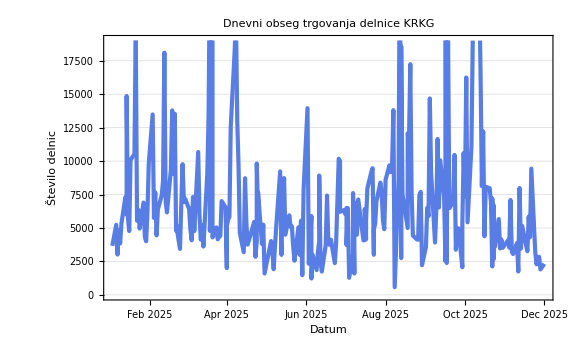

```mathematica
DateListPlot[Transpose[{dates,volume}],PlotTheme->"Business",ImageSize->Large,PlotLabel->"Dnevni obseg trgovanja delnice KRKG",AxesLabel->{"Datum","Število delnic"}]
```

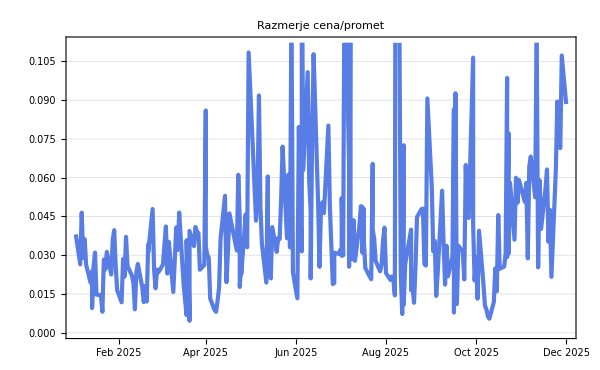
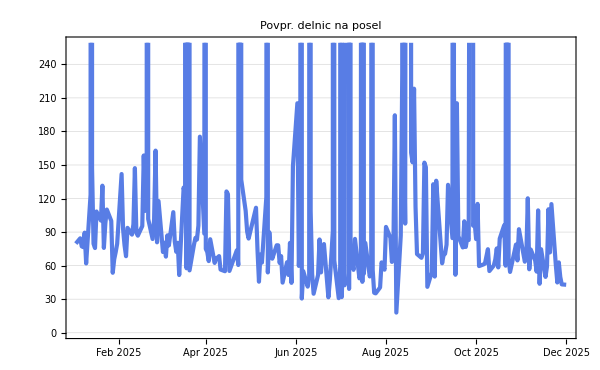

```mathematica
Row[{DateListPlot[Transpose[{dates,N[last/volume]}],ImageSize->600,PlotLabel->"Razmerje cena/promet",PlotTheme->"Business"],DateListPlot[Transpose[{dates,N[volume/trades]}],ImageSize->600,PlotLabel->"Povpr. delnic na posel",PlotTheme->"Business"]}]
```

Na podlagi prikazanih grafov lahko zaključimo, da je bila delnica KRKG v letu 2025 večinoma v rastočem trendu, občasno pa so se pojavila tudi izrazitejša nihanja. Spreminjanje prometa in števila poslov kaže na različno aktivnost vlagateljev skozi leto.

Spodnji histogram prikazuje porazdelitev zaključnih cen delnice KRKG v letu 2025. Na podlagi grafa lahko opazujemo, v katerem cenovnem območju se je delnica gibala najpogosteje.

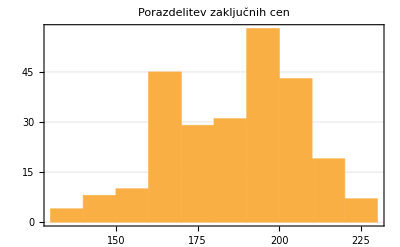

```mathematica
Histogram[last,PlotTheme->"Business",PlotLabel->"Porazdelitev zaključnih cen"]
```

```mathematica
Grid[{{"Najnižja cena",Min[last]},{"Najvišja cena",Max[last]},{"Povprečna cena",Mean[last]},{"Mediana",Median[last]}},Frame->All]
```

Najnižja cena | 138.5
Najvišja cena | 221.
Povprečna cena | 186.437
Mediana | 189.75

```mathematica
dataset=Dataset[Map[<|"Datum"->#[[1]],"Cena"->#[[2]]|>&,Transpose[{dates,last}]]];

Grid[{{"5 najvišjih zaključnih cen"},{dataset[Query[TakeLargestBy["Cena",5]]]},{"5 najnižjih zaključnih cen"},{dataset[Query[TakeSmallestBy["Cena",5]]]}},Frame->All,Alignment->Left]
```

5 najvišjih zaključnih cen

5 najnižjih zaključnih cen

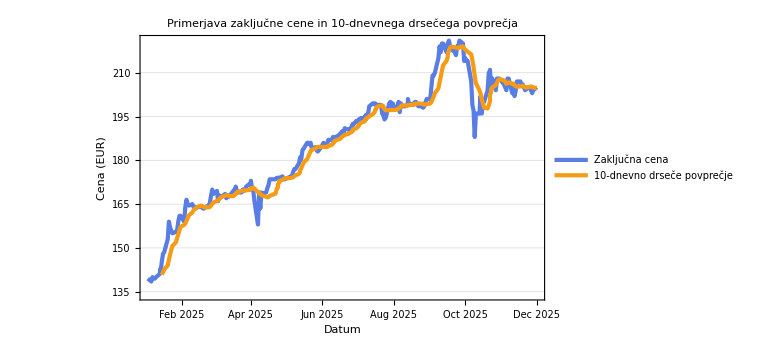

```mathematica
movingAvg=MovingAverage[last,10];

DateListPlot[{Transpose[{dates,last}],Transpose[{dates[[10;;]],movingAvg}]},PlotTheme->"Business",PlotLegends->{"Zaključna cena","10-dnevno drseče povprečje"},PlotLabel->"Primerjava zaključne cene in 10-dnevnega drsečega povprečja",AxesLabel->{"Datum","Cena (EUR)"},ImageSize->Large]
```

## Simulacija naključnega investitorja

V tem delu simuliramo vlagatelja, ki naključno izbere dan nakupa in kasnejši dan prodaje delnice. Izračunamo njegov dobiček oziroma izgubo ter nato simulacijo večkrat ponovimo.

```mathematica
buy=RandomInteger[{1,Length[last]-1}];
sell=RandomInteger[{buy+1,Length[last]}];

buyPrice=last[[buy]];
sellPrice=last[[sell]];

profit=sellPrice-buyPrice;

Grid[{{"Nakupni dan",dates[[buy]]},{"Prodajni dan",dates[[sell]]},{"Nakupna cena",buyPrice},{"Prodajna cena",sellPrice},{"Dobiček/izguba",profit}},Frame->All]
```

Nakupni dan | Thu 5 Jun 2025 00:00:00GMT+2
Prodajni dan | Fri 27 Jun 2025 00:00:00GMT+2
Nakupna cena | 185.5
Prodajna cena | 192.
Dobiček/izguba | 6.5

Da dobimo bolj realističen vpogled v uspešnost naključnega trgovanja, simulacijo ponovimo 1000-krat. Vsaka simulacija predstavlja en naključen nakup in kasnejšo prodajo delnice.

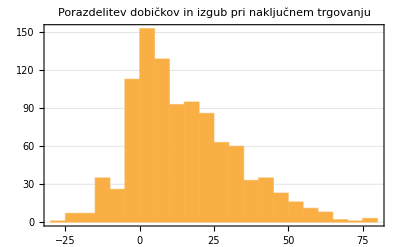

Povprečni rezultat | 14.4395
Največji dobiček | 77.
Največja izguba | -29.
Dobičkonosnih poslov | 779
Izgubnih poslov | 189

```mathematica
RandomTradeProfit[prices_]:=Module[{buy,sell},buy=RandomInteger[{1,Length[prices]-1}];
sell=RandomInteger[{buy+1,Length[prices]}];
prices[[sell]]-prices[[buy]]]

profits=Table[RandomTradeProfit[last],{1000}];

Histogram[profits,PlotTheme->"Business",PlotLabel->"Porazdelitev dobičkov in izgub pri naključnem trgovanju"]

Grid[{{"Povprečni rezultat",Mean[profits]},{"Največji dobiček",Max[profits]},{"Največja izguba",Min[profits]},{"Dobičkonosnih poslov",Count[profits,_?(#>0&)]},{"Izgubnih poslov",Count[profits,_?(#<0&)]}},Frame->All]
```

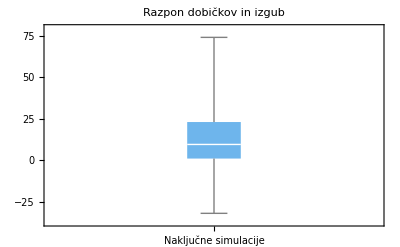

```mathematica
BoxWhiskerChart[profits,ChartLabels->{"Naključne simulacije"},PlotLabel->"Razpon dobičkov in izgub",ChartStyle->"Pastel"]
```

BoxWhiskerChart prikazuje razpon dobičkov in izgub pri 1000 naključnih simulacijah nakupa in prodaje delnice KRKG.

```mathematica
PieChart[{Count[profits,_?(#>0&)],Count[profits,_?(#<=0&)]},ChartLabels->{"Dobiček","Izguba"},PlotLabel->"Delež uspešnih in neuspešnih poslov"]
```

-Graphics-

## Interaktivna aplikacija

Interaktivna aplikacija uporabniku omogoča izbiro dneva nakupa in dneva prodaje delnice. Program izračuna dobiček oziroma izgubo ter prikaže gibanje tečaja med izbranima dnevoma.

```mathematica
Manipulate[Module[{dobicek},dobicek=last[[prodaja]]-last[[nakup]];
Column[{Grid[{{"Datum nakupa",dates[[nakup]]},{"Datum prodaje",dates[[prodaja]]},{"Dobiček (EUR)",NumberForm[dobicek,{6,2}]}},Frame->All],DateListPlot[Transpose[{dates[[nakup;;prodaja]],last[[nakup;;prodaja]]}],Joined->True,PlotTheme->"Business",PlotLabel->"Gibanje cene med nakupom in prodajo",AxesLabel->{"Datum","Cena (EUR)"},ImageSize->Large]}]],{{nakup,20,"Dan nakupa"},1,Length[last]-1,1},{{prodaja,150,"Dan prodaje"},Dynamic[nakup+1],Length[last],1}]
```